#### Kirill Zakharov Best mean-square approximation polynomial

fun - исходная функция
n - степень аппроксиманта

```mathematica
hermite[n_]:=(-1)^n*ⅇ^(x^2)*D[ⅇ^(-x^2),{x,n}]/√(2^n n!√Pi)//FullSimplify
aCoefficient[fun_,n_]:=∫_(-∞)^(+∞) fun*ⅇ^(-x^2)*hermite[n]ⅆx
approximant[fun_,n_]:=Total[Table[N@hermite[k]*aCoefficient[fun,k]//N,{k,0,n}]]//FullSimplify
```

#### Test 1

```mathematica
polynomial=approximant[x^2,2];
```

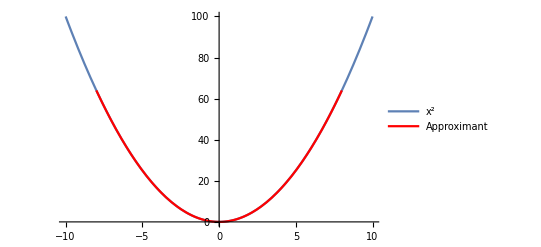

```mathematica
Show[{Plot[x^2,{x,-10,10},PlotLegends->{"x^2"}],Plot[polynomial/.x->k,{k,-8,8},PlotStyle->Red,PlotLegends->{"Approximant"}]}]
```

#### Test 2

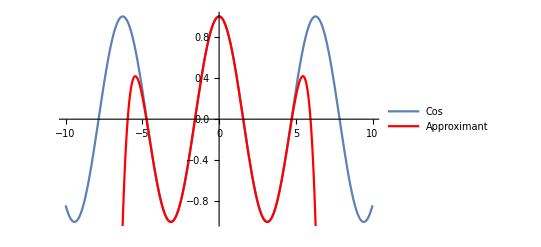

```mathematica
polynomial1=approximant[Cos[x],10];
Show[{Plot[Cos[x],{x,-10,10},PlotLegends->{"Cos"}],Plot[polynomial1/.x->k,{k,-8,8},PlotStyle->Red,PlotLegends->{"Approximant"}]}]
```

Увеличив степень полинома, получаем большую точность.

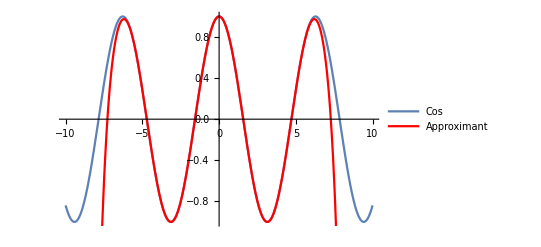

```mathematica
polynomial12=approximant[Cos[x],15];
Show[{Plot[Cos[x],{x,-10,10},PlotLegends->{"Cos"}],Plot[polynomial12/.x->k,{k,-8,8},PlotStyle->Red,PlotLegends->{"Approximant"}]}]
```

#### Test 3

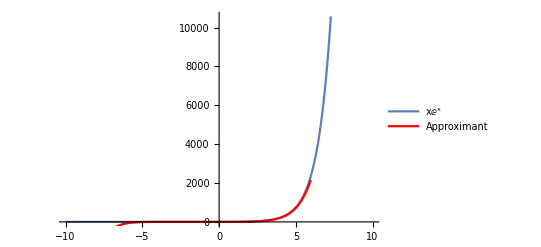

```mathematica
polynomial2=approximant[x ⅇ^x,9];
Show[{Plot[x ⅇ^x,{x,-10,10},PlotLegends->{"xⅇ^x"}],Plot[polynomial2/.x->k,{k,-8,8},PlotStyle->Red,PlotLegends->{"Approximant"}]}]
```